Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

6 - 11 General Solution
Find a general solution of the ODE y’’+ω^2y = r(t)
with r(t) as given below.

6. r(t) = sin αt + sin βt, ω^2 ≠ α^2, β^2

```mathematica
Clear["Global`*"]
```

```mathematica
r[t_]:=Sin[αt]+Sin[βt] /;{{ω^2≠α^2},{ω^2≠β^2}}
```

```mathematica
DSolve[y''[t]+ω^2 y[t]==r[t],y[t],t]
```

{{y[t]→C[1] Cos[t ω]+Cos[t ω] ∫_1^t -(r[K[1]] Sin[ω K[1]])/ωⅆK[1]+C[2] Sin[t ω]+(∫_1^t (Cos[ω K[2]] r[K[2]])/ω ⅆK[2]) Sin[t ω]}}

An even-numbered problem. Is the answer correct? Can’t check it.

7. r(t) = sin t, ω = 0.5, 0.9, 1.1, 1.5, 10

```mathematica
Clear["Global`*"]
```

```mathematica
r[t_]:=Sin[t]
eq1 =DSolve[y''[t]+ω^2 y[t]==r[t],y[t],t]
```

{{y[t]→C[1] Cos[t ω]+C[2] Sin[t ω]+(Cos[t ω]^2 Sin[t]+Sin[t] Sin[t ω]^2)/(-1+ω^2)}}

```mathematica
eq2 =eq1 /.(Cos[t ω]^2 Sin[t]+Sin[t] Sin[t ω]^2)/(-1+ω^2)->Sin[t]/(-1+ω^2)
```

{{y[t]→C[1] Cos[t ω]+Sin[t]/(-1+ω^2)+C[2] Sin[t ω]}}

Above: making a trig identity substitution by hand to conform the green cell to the text answer. The sequence of ω s makes it look like a table could be built, but not of the solution function, because the arbitrary constants blur everything. Instead the text focuses on the particle 1/(-1+ω^2), listing the calculated values for each ω.

```mathematica
ome[ω_]=1/(-1+ω^2)
```

1/(-1+ω^2)

```mathematica
m=Table[ome[ω],{ω,{0.5,0.9,1.1,1.5,10}}]
```

{-1.33333,-5.26316,4.7619,0.8,1/99}

```mathematica
N[TableForm[{{0.5,-1.3333333333333333},{0.9,-5.263157894736843},{1.1,4.761904761904757},{1.5,0.8},{10,1/99}},TableHeadings->{{},{"ω","m[ω]"}}]]
```

| ω | m[ω]
 | 0.5 | -1.33333
 | 0.9 | -5.26316
 | 1.1 | 4.7619
 | 1.5 | 0.8
 | 10. | 0.010101

The above matches the text, though the table construction seemed more time-consuming than profitable.

11.  r(t) = Piecewise[{{-1, if -π<t<0}, {1, if 0<t<π}}] |ω|≠1,3,5,...

```mathematica
Clear["Global`*"]
```

```mathematica
r[t_] =Piecewise[{{-1, -π<t<0},{1,0<t<π}}]
```

```mathematica
Piecewise[{{-1, -π<t<0}, {1, 0<t<π}, {0, True}}]
```

First r[t] is considered by finding its Fourier series.

```mathematica
e3=ExpToTrig[FourierSeries[Piecewise[{{-1,-π<t<0},{1,0<t<π}}],t,6]]
```

(4 Sin[t])/π+(4 Sin[3 t])/(3 π)+(4 Sin[5 t])/(5 π)

The above doesn't look bad at all. The general term is 4/(n π)Sin[n t], with n = 1, 3, 5 ... In the text example, the general term of the Fourier series is set equal to the ODE without apology, so I will do it too.  At this point in the problem, I am supposed to switch over to considering the ODE, including that series general term for r[t].

```mathematica
eq1 =FullSimplify[DSolve[y''[t]+ω^2 y[t]==4/(n π)Sin[n t],y[t],t]]
```

{{y[t]→C[1] Cos[t ω]-(4 Sin[n t])/(n^3 π-n π ω^2)+C[2] Sin[t ω]}}

```mathematica
eq11 =eq1  /.n->1
```

{{y[t]→C[1] Cos[t ω]-(4 Sin[t])/(π-π ω^2)+C[2] Sin[t ω]}}

```mathematica
eq13 = eq1 /. n->3
```

{{y[t]→C[1] Cos[t ω]-(4 Sin[3 t])/(27 π-3 π ω^2)+C[2] Sin[t ω]}}

```mathematica
eq15 = eq1 /. n->5
```

{{y[t]→C[1] Cos[t ω]-(4 Sin[5 t])/(125 π-5 π ω^2)+C[2] Sin[t ω]}}

This seemed to be going so well. But I could not (quite) get to the text answer. The yellow cells should show the text answer, but the central term of the text answer presents the model 4/π Sin[n t]/(ω^2-(4n-1)^2),  instead of the yellow 4/(n π)Sin[n t]/(n^2-ω^2), and I don’t understand this result. I checked the integration in Symbolab, and it agreed with Mathematica as far as the integration is concerned. Certainly it is possible the text answer is correct.

13 - 16 Steady-State Damped Oscillations
Find the steady-state oscillations of y’’+cy’+y = r(t) with c>0 and r(t) as given. Note that the spring constant is k=1. Show the details. In probs. 14 - 16 sketch r(t).

13. r(t) = ∑_(n=1)^N (a_n cos nt + b_n sin nt)

```mathematica
Clear["Global`*"]
```

Here r[t] is already a series. r[t_]=∑_(n=1)^N (a Cos[n t]+b Sin[n t]). Using a method seen in the solutions manual, I will drop the subscripts of the coefficients a and b. (This problem is being solved after finishing problem 15, for which s.m. assistance was available.) I will consider r[t] to be a single term of the series.

```mathematica
r[t_]= a Cos[n t] + b Sin[n t]
```

a Cos[n t]+b Sin[n t]

```mathematica
r'[t]
```

b n Cos[n t]-a n Sin[n t]

```mathematica
r''[t]
```

-a n^2 Cos[n t]-b n^2 Sin[n t]

```mathematica
partic = r''[t]+c r'[t]+r[t]
```

a Cos[n t]-a n^2 Cos[n t]+b Sin[n t]-b n^2 Sin[n t]+c (b n Cos[n t]-a n Sin[n t])

```mathematica
eq1 = Simplify[partic]
```

(a+b c n-a n^2) Cos[n t]+(b-a c n-b n^2) Sin[n t]

For this problem, evidently the RHS will have both sine and cosine terms. The value of N is unknown, but it could encompass any number of 2π cycles. The coefficients must keep the same ratios at all points of the trig circle, so I take the guess that A_n will be solved when the function is at zero (cosine function is max), and B_n will be solved
when the function is at π/2 (sine function is max). So eq2 will be for A_n:

```mathematica
eq2=Solve[{a+b*c*n-a*n^2==1,b-a*c*n-b*n^2==0},{a,b}]
```

{{a→-(-1+n^2)/(1-2 n^2+c^2 n^2+n^4),b→(c n)/(1-2 n^2+c^2 n^2+n^4)}}

To assemble A_n I suppose that all I need to do is multiply the numerators by the relevant coefficients and add these two together. (I can already check the 'D_n' value, the denominator, with the text and confirm that it agrees.)

```mathematica
bigA=Simplify[-((-1+n^2)asubn)/(1-2 n^2+c^2 n^2+n^4)+((c n)bsubn)/(1-2 n^2+c^2 n^2+n^4)]
```

(asubn+bsubn c n-asubn n^2)/(1+(-2+c^2) n^2+n^4)

The method works for A_n above, which agrees with the text. Now to try to figure out B_n, which I predict must come into alignment at trig π/2:

```mathematica
eq3 =Solve[{a+b*c*n-a*n^2==0,b-a*c*n-b*n^2==-1},{a,b}]
```

{{a→(c n)/(1-2 n^2+c^2 n^2+n^4),b→-(1-n^2)/(1-2 n^2+c^2 n^2+n^4)}}

```mathematica
BigB=Simplify[((c n)asubn)/(1-2 n^2+c^2 n^2+n^4)-((-1+n^2)bsubn)/(1-2 n^2+c^2 n^2+n^4)]
```

(bsubn+asubn c n-bsubn n^2)/(1+(-2+c^2) n^2+n^4)

The method works for B_n too, except that in order to get the sign of a_nto agree with the text, it was necessary to choose -π/2 as the point of evaluation, so that the a_n part of the B_n ensemble could be positive in sign. I don’t know how to interpret that requirement.

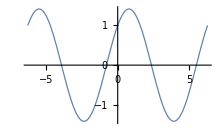

```mathematica
Plot[ Cos[ t]+ Sin[ t], {t,-2π,2π},PlotStyle->Thickness[0.004]]
```

The plot (above) does not look quite as expected. I feel I should emphasize that the described solution method is largely speculation.

15. r(t) =  t(π^2-t^2)  if -π<t<π , and r(t+2π) = r(t)

This problem is covered in the s.m.. The observation, made there and visible from the problem description, is that the function r[t] is odd and that the function’s cycle is 2π. At this point I check the Fourier series.

```mathematica
Clear["Global`*"]
```

```mathematica
eq1=FourierSeries[t(π^2-t^2),t,1]
```

6 ⅈ ⅇ^(-ⅈ t)-6 ⅈ ⅇ^(ⅈ t)

```mathematica
eq2 =ExpToTrig[6 ⅈ ⅇ^(-ⅈ t)-6 ⅈ ⅇ^(ⅈ t)]
```

12 Sin[t]

So at this point I know the form of the output series. No cosine term. I don’t take the ‘12’ too seriously, it is still subject to some variation.

The method of finding a particular solution in example 1 on p. 493 sees it as y’’+cy’+y=b_n sin nt.  Here the s.m. makes reference to example 1, where in a similar situation the y_p is set to y= A cos nt + B sin nt. The motivation for this is an entry in Table 2.1, p. 82, “Method of Undetermined Coefficients, where, upon finding r[t] equal to k sin ωx, a preliminary choice for y_p(x) is taken as K cos ωx +M sin ωx. So at this point I have [1]: y=A cos nt + B sin nt, and I go on to assign [2]: y’=-A sin nt + B cos nt, and also [3]: y’’=-A cos nt -B sin nt.

```mathematica
partic= (y''[t]+c y'[t] + y[t])
```

y[t]+c y'[t]+y''[t]

partic is the LHS

```mathematica
r[t] =A Cos[n t] + B Sin[n t] +c(-n A Sin[n t] + n B Cos[n t])-n^2 A Cos[n t]-n^2 B Sin[n t]
```

A Cos[n t]-A n^2 Cos[n t]+B Sin[n t]-B n^2 Sin[n t]+c (B n Cos[n t]-A n Sin[n t])

r[t] is the consolidation of plugging values of the 3 equations into LHS and adding them up.

```mathematica
Simplify[r[t]]
```

(A+B c n-A n^2) Cos[n t]+(B-A c n-B n^2) Sin[n t]

Now it is time to solve for coefficients of the r[t] complex.  Final coefficient of cosine must be zero (since it doesn’t appear in final r) and final coefficient of sine must be b_n. As for n, it can vary in series fashion. It is necessary to humor Mathematica a bit, as for instance not using variables beginning with captitals, and, for just this once, eschewing subscripts (m is standing in for b_n);

```mathematica
eq3=Solve[{a+b*c*n-a*n^2==0,b-a*c*n-b*n^2==m},{a,b}]
```

{{a→-(c m n)/(1-2 n^2+c^2 n^2+n^4),b→-(m (-1+n^2))/(1-2 n^2+c^2 n^2+n^4)}}

Solve does the solve thing, and sets the denominator to the correct value of D_(n.) In the cell below, it will be done in the determinant way.

```mathematica
dee =Det[({{1-n^2, c n}, {-c n, 1-n^2}})]
```

1-2 n^2+c^2 n^2+n^4

The s.m. now goes on to find A and B, using determinants, but will it thereby find what Solve came up with above? The current step is to find b_(n,)which Mathematica has not yet found, and which it cannot find by modifying eq3 for the search. But the s.m. goes back to a table on page 487, where is says that an odd function with period 2π should follow the formula b_n=2/π∫_0^(2π) f(x)sin nxⅆx   and n=1,2,... Okay, I’ll follow.

```mathematica
bn=2/π Integrate[t(π^2-t^2)Sin[n t], {t,0,π}]
```

(2 (-6 n π Cos[n π]-2 (-3+n^2 π^2) Sin[n π]))/(n^4 π)

```mathematica
int = bn /.Cos[n π]->(-1)^n
```

(2 (-6 (-1)^n n π-2 (-3+n^2 π^2) Sin[n π]))/(n^4 π)

```mathematica
Subscript[b, n] = int /.Sin[n π]->0
```

-(12 (-1)^n)/n^3

With two invaluable trig substitutions provided by s.m., b_n is determined, above, green. I now have the value of ‘m’ in eq3, and I want to use it to find the total A, using the numerator of the ‘a’ part of eq3.

```mathematica
aaa=-cn(Subscript[b, n])
```

-cn b_n

```mathematica
aaaa =aaa/.Subscript[b, n]->-(12 (-1)^n)/n^3
```

(12 (-1)^n cn)/n^3

```mathematica
aaaaa=aaaa/dee
```

(12 (-1)^n cn)/(n^3 (1-2 n^2+c^2 n^2+n^4))

Above is the final value of A, which agrees with the text answer.

```mathematica
bbb=- (-1+n^2)Subscript[b, n]
```

(1-n^2) b_n

```mathematica
bbbb=bbb/.Subscript[b, n]-> -(12 (-1)^n)/n^3
```

-(12 (-1)^n (1-n^2))/n^3

```mathematica
bbbbb=bbbb/dee
```

-(12 (-1)^n (1-n^2))/(n^3 (1-2 n^2+c^2 n^2+n^4))

Above is the final answer of B, which agrees with the text answer. (Note that (-1)^n resolves to (-1)^(n+1).) This problem also requires a sketch of r[t].

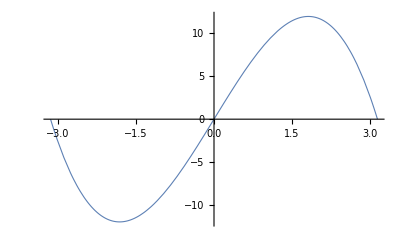

```mathematica
rtplot = Plot[t(π^2-t^2), {t,-π,π},PlotStyle->Thickness[0.002]]
```

17 - 19 RLC-circuit.
Find the steady state current I(t) in the RLC-circuit in figure 275, where R=10 Ω, L=1 H, C=10^-1 F and with E(t) V as follows and periodic with period 2π. Graph or sketch the first four partial sums. Note that the coefficients of the solution decrease rapidly. Hint. Remember that the ODE contains E'(t), not E(t), cf. section 2.9.

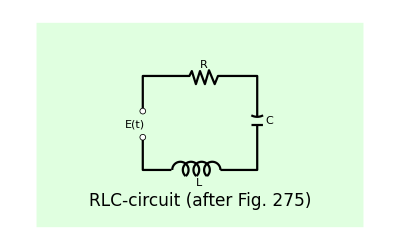

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,2.5}]},{Thickness[0.004],Line[{{1.3,1.1},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.25}}]},{Thickness[0.004],Line[{{2.63,1.25},{2.77,1.25}}]},{Thickness[0.004],Circle[{2.7,1.5},0.15,{-π/2-0.5,-π/2+0.5}]},{Thickness[0.004],Line[{{2.7,1.35},{2.7,1.85},{2.22,1.85},{2.18,1.75},{2.11,1.92},{2.06,1.75},{2,1.91},{1.95,1.75},{1.9,1.91},{1.87,1.85},{1.3,1.85},{1.3,1.42}}]},{Disk[{1.3,1.42},0.04]},{White,Disk[{1.3,1.42},0.03]},{Disk[{1.3,1.1},0.04]},{White,Disk[{1.3,1.1},0.03]},{Text[Style["E(t)",Medium],{1.2,1.26}]},{Text[Style["R",Medium],{2.05,1.99}]},{Text[Style["L",Medium],{1.99,0.54}]},{Text[Style["RLC-circuit (after Fig. 275)",17],{2,0.32}]},{Text[Style["C",Medium],{2.85,1.3}]}},Axes->False]
```

17. E[t]=Piecewise[{-50 t^2,-π<t<0},{50 t^2,0<t<π}]

```mathematica
Clear["Global`*"]
```

First, setting up the electrical state space model just as if the domain were not piecewise.

```mathematica
eqns={eL q''[t]+aR q'[t]+1/cC q[t]==Vee[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{Vee[t],0}},{q'[t]},t]
```

010-1/(cC eL)-aR/eL1/eL010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

And putting in the capacitance, inductance, and resistance from the problem description.

```mathematica
mw=m1/.{cC->0.1,eL->1,aR->10}
```

010-10.-101010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

And getting an output response for the interval where the voltage is negative. Note that this is in an interval where t is negative. What does a negative time value represent? I don’t really blame Mathematica for dumping the output into a single point, probably zero.

```mathematica
outz=OutputResponse[{mw},-50 t^2,{t,-π,0}]
```

{InterpolatingFunction[{{0., 0.}}, <>][t]}

And another output response for the interval where the voltage (and time) is positive.

```mathematica
outzp=OutputResponse[{mw},50 t^2,{t,0,π}]
```

{InterpolatingFunction[{{0., 3.14159}}, <>][t]}

And devising a plot for the positive t section. If this was a serious project, I would look into the possibility of moving everything to the right so that all time values would be positive.

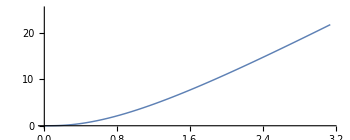

```mathematica
p1=Plot[{outzp},{t,0,π},ImageSize->350,AspectRatio->0.4,PlotRange->{{-0.001,π},{-0.005,25}},PlotStyle->Thickness[0.003],GridLines->All]
```

```mathematica
NIntegrate[outzp,{t,0,3}]
```

{23.6933}

```mathematica
an=-400/(n^2 π)
```

-400/(n^2 π)

```mathematica
dn=(n^2-10)^2+100 n^2
```

100 n^2+(-10+n^2)^2

```mathematica
han=N[Table[((10-n^2)an)/dn,{n,1,6}]]
```

{-6.33103,-0.438041,-0.0157016,0.0291849,0.0280346,0.0215052}

```mathematica
hbn=N[Table[((10n)an)/dn,{n,1,6}]]
```

{-7.03447,-1.46014,-0.471047,-0.194566,-0.0934488,-0.0496274}

```mathematica
eye=N[50+han[[1]]Cos[3]+hbn[[1]]Sin[3]+han[[3]]Cos[9]+hbn[[3]]Sin[9]]
```

55.0951

There is something obviously wrong with this problem somewhere. There is an absurdly large gap between what I am coming up (for steady state current) using the text answer and when using the state space model. This is in gross contrast to the results in section 2.9, when the state space model was on the money. However, back then the function went into cycles, whereas here it just rises. The problem description describes the function as 2π periodic, but I see no tendency to operate in a cycle.

19. E[t]=Piecewise[{200t(π^2 t^2),-π<t<π},{0,-∞<t≤-π}]

```mathematica
Clear["Global`*"]
```

First, setting up the electrical state space model just as if the domain were not piecewise.

```mathematica
eqns={eL q''[t]+aR q'[t]+1/cC q[t]==Vee[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{Vee[t],0}},{q'[t]},t]
```

010-1/(cC eL)-aR/eL1/eL010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

And putting in the capacitance, inductance, and resistance from the problem description.

```mathematica
mw=m1/.{cC->0.1,eL->1,aR->10}
```

010-10.-101010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

And getting an output response for the interval where the voltage is non-zero. Note that part of this interval occurs where t is negative. What does a negative time value represent? The way Mathematica handles this situation is to ignore the negative time interval.

```mathematica
outz=OutputResponse[{mw},200t(π^2 t^2),{t,-π,π}]
```

{InterpolatingFunction[{{0., 3.14159}}, <>][t]}

```mathematica
NIntegrate[outz,{t,0,3}]
```

{2282.5}

And another output response for the interval where the voltage is zero and the time is positive.

```mathematica
outz0=OutputResponse[{mw},0,{t,π,20}]
```

{InterpolatingFunction[{{0., 20.}}, <>][t]}

And devising a plot for the positive t section. If this was a serious project, I would look into the possibility of moving everything to the right so that all time values would be positive. The plot below looks reasonable to me.

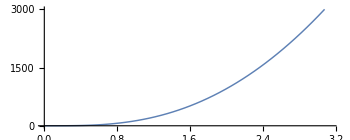

```mathematica
p1=Plot[{outz},{t,0,π},ImageSize->350,AspectRatio->0.4,PlotRange->{{-0.001,π},{-0.005,3000}},PlotStyle->Thickness[0.003],GridLines->All]
```

```mathematica
Subscript[D, n]=(10-n^2)^2+100 n^2
```

100 n^2+(10-n^2)^2

```mathematica
Subscript[A, n]=(-1)^(n+1)(2400(10-n^2))/(n^2 Subscript[D, n])
```

(2400 (-1)^(1+n) (10-n^2))/(n^2 (100 n^2+(10-n^2)^2))

```mathematica
Subscript[B, n]=(-1)^(n+1)24000/(n Subscript[D, n])
```

(24000 (-1)^(1+n))/(n (100 n^2+(10-n^2)^2))

```mathematica
eye=N[Simplify[ComplexExpand[Re[Sum[Subscript[A, n] Cos[n t]+Subscript[B, n] Sin[n t],{n,1,∞}]]]]];
```

```mathematica
eyet3=eye/.t->3
```

-89.8515

Way off base. See the comments in problem 17.